#### This notebook contains simulations of STIRAP for transfer of NaCs molecules from a Feshbach state to absolute ground state, via a fast-scattering intermediate. Several different versions of the simulation are below: 1. A simple 3-state system with non-Hermitian term accounting for loss from the excited state 2. Simulation of dark resonance, with coinciding square pump and stokes pulses 3. Model accounting for Stark shift induced by nearby excited state 4. Master equation based model accounting for phase-noise induced decay of coherence (numerically buggy)

### Define Rabi rates for Stokes and Pump, with pulse power and timing parameters

```mathematica
(*Ωs = 2 π PS*10^6*Exp[-0.5((t - t1)/w)^2](*Piecewise[{{1 - Abs[(t - t1)/(w)],Abs[t -t1]<w}},0]*);
Ωp = 2 π  PP*10^6*Exp[-0.5((t - 20*10^-6)/w)^2]*)(*Piecewise[{{1 - Abs[(t - 20*10^-6)/(w)],Abs[t -20*10^-6]<w}},0]*)
Ωs = 2 π PS*10^6*Piecewise[{{1 -Sqrt[((t - t1)/(w))^2 + 0.01],Abs[t -t1]<Sqrt[0.99]*w}},0];
Ωp = 2 π  PP*10^6*Piecewise[{{1 -Sqrt[((t - 30*10^-6)/(w))^2 + 0.01],Abs[t -30*10^-6]<Sqrt[0.99]*w}},0];
θ[t_] = ArcTan[Ωp/Ωs] ;
dθ = D[θ[t] ,t];
vars =  {PS -> x ,t1 -> y,w->z, PRatio -> r};

(*Plot pulses envelopes and mixing angle over time*)
Manipulate[Plot[{Ωp /. {PS ->StokesPower ,t1 ->tP,w->width, PP -> PumpPower},Ωs /. {PS ->StokesPower ,t1 ->tP,w->width, PP -> PumpPower}},{t,0,50*10^-6},PlotLegends->  {"Ωp","Ωs"},PlotRange->All,ImageSize->Large],{StokesPower,0.1,20},{tP,0*10^-6,30*10^-6},{width,1*10^-6,10*10^-6},{PumpPower,0.1,20}]
SetSystemOptions["CheckMachineUnderflow"->False];
```

### 1. Three-level system model: define Schroedinger equation and numerically solve

This is a simple non-Hermitian Hamiltonian model of STIRAP accounting  for decay at rate γ from the intermediate state

```mathematica
init=P[0]=={1,0,0,0}
```

{p1[0],p2[0],p3[0],p4[0]}=={1,0,0,0}

```mathematica
init=P[0]=={1,0,0,0};
P[t_]={p1[t],p2[t],p3[t],p4[t]};
H[t_]={{0,Ωp/2,(3.5 Ωp)/2,0},{Ωp/2,2 π Δ-ⅈ 2 π γ,0,Ωs/2},{(3.5 Ωp)/2,0,2 π (Δ+Δ1)-ⅈ 2 π γ,0},{0,Ωs/2,0,2 π δ}};
MatrixForm[H[t]];
SE=ⅈ P'[t]==H[t].P[t];
```

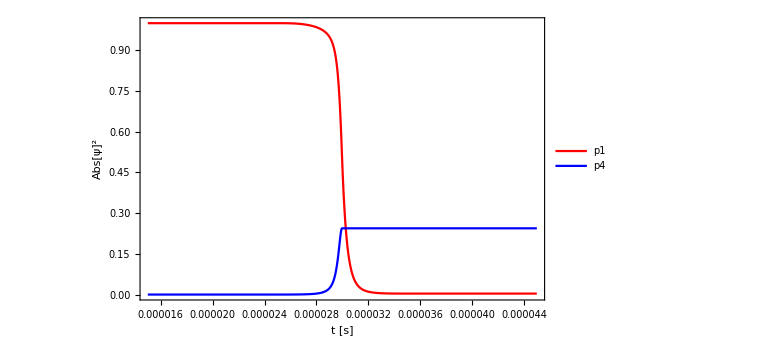

```mathematica
PSoln=ParametricNDSolve[{SE/.γ->100 10^6,init},{p1,p2,p3,p4},{t,0,50/10^6},{t1,w,PS,PP,δ,Δ,Δ1},PrecisionGoal->5];
Plot[{Evaluate[Abs[p1[25/10^6,5/10^6,250,10,0,0,3.4 10^9][t]]^2/.PSoln],Evaluate[Abs[p4[25/10^6,5/10^6,250,10,0,0,3.4 10^9][t]]^2/.PSoln]},{t,15/10^6,45/10^6},ImageSize->Large,PlotLegends->{"p1","p4"},FrameLabel->{"t [s]",Abs[ψ]^2},PlotRange->All]
```

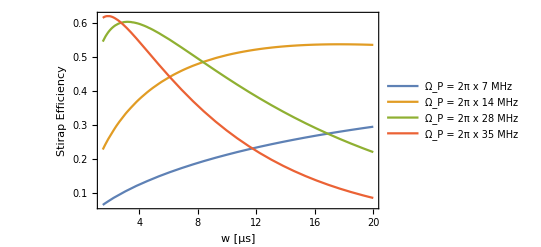

```mathematica
PSoln = ParametricNDSolve[{SE /. γ ->90*10^6,init},{p1,p2,p3,p4},{t,0,50*10^-6},{t1,w, PS, PP,δ,Δ,Δ1 },PrecisionGoal->10];
(*Plot[{Abs[p4[30*10^-6 -w*10^-6,w*10^-6,250,20,0,0,3.4*10^9][30*10^-6]]^2/. PSoln},{w,2,20}, AxesLabel->{"w [us]", Abs[ψ]^2}, PlotRange->All,PerformanceGoal->"Speed"]*)
Plot[{Abs[p4[30*10^-6 -w*10^-6,w*10^-6,250,7,-0.1*10^6,0,3.4*10^9][50*10^-6]]^2/. PSoln,Abs[p4[30*10^-6 -w*10^-6,w*10^-6,250,14,-0.1*10^6,0,3.4*10^9][50*10^-6]]^2/. PSoln, Abs[p4[30*10^-6 -w*10^-6,w*10^-6,250,28,-0.1*10^6,0,3.4*10^9][50*10^-6]]^2/. PSoln,Abs[p4[30*10^-6 -w*10^-6,w*10^-6,250,35,-0.1*10^6,0,3.4*10^9][50*10^-6]]^2/. PSoln},{w,1.5,20}, AxesLabel->{"w [μs]","Stirap Efficiency"}, PlotRange->All,PerformanceGoal->"Speed",PlotLegends->{"Ω_P = 2π x 7 MHz","Ω_P = 2π x 14 MHz","Ω_P = 2π x 28 MHz","Ω_P = 2π x 35 MHz"},LabelStyle->{FontSize->18,FontFamily->"Times",Black},PlotStyle->Thick]
```

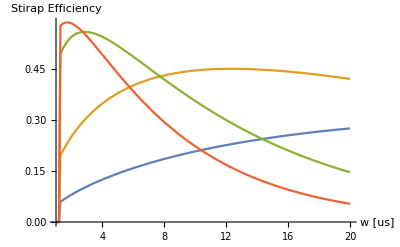

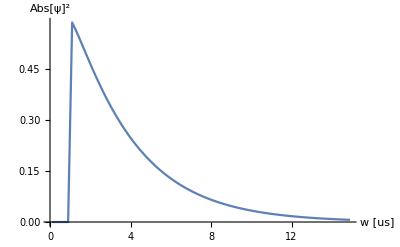

```mathematica
PSoln = ParametricNDSolve[{SE /. γ ->90*10^6,init},{p1,p2,p3,p4},{t,0,50*10^-6},{t1,w, PS, PP,δ,Δ,Δ1 },PrecisionGoal->15];
(*Plot[{Abs[p4[30*10^-6 -w*10^-6,w*10^-6,250,20,0,0,3.4*10^9][30*10^-6]]^2/. PSoln},{w,2,20}, AxesLabel->{"w [us]", Abs[ψ]^2}, PlotRange->All,PerformanceGoal->"Speed"]*)
ListLinePlot[Table[{w,Abs[p4[30*10^-6 -0.99w*10^-6,w*10^-6,250,50,0.2*10^6,0,3.4*10^9][45*10^-6]]^2/. PSoln},{w,0.1,15,0.2}], AxesLabel->{"w [us]", Abs[ψ]^2}, PlotRange->All,PerformanceGoal->"Speed"]
```

#### Plot parameters for 3-level model

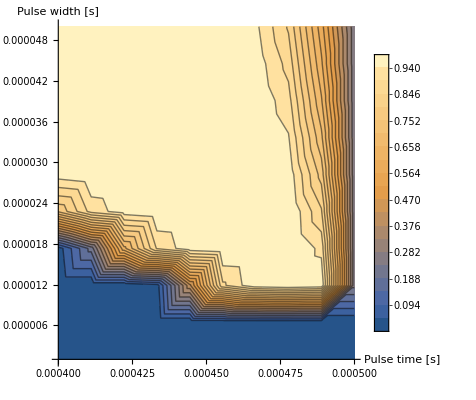

```mathematica
ContourPlot[Evaluate[Abs[p3[t1,w,0.2,20][1.5*10^-3]]^2/. PSoln] ,{t1,400*10^-6,500*10^-6},{w,1*10^-6,50*10^-6},PlotLegends->Automatic,Axes -> True,Frame->False,Exclusions->None,AxesLabel->{"Pulse time [s]","Pulse width [s]"}, PerformanceGoal->"Speed", Contours->20]
```

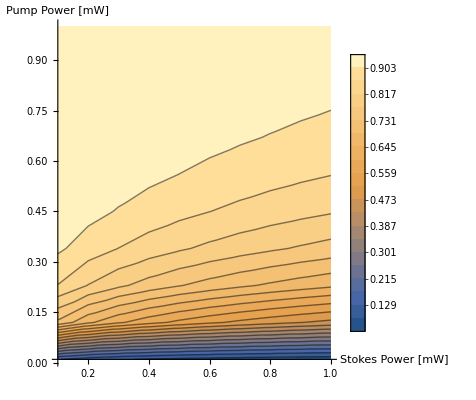

```mathematica
ContourPlot[Evaluate[Abs[p3[450*10^-6,30*10^-6,StokesPower,PumpPower][600*10^-6]]^2/. PSoln] ,{StokesPower,0.1,1},{PumpPower,0.01,1},PlotLegends->Automatic,Exclusions->None,Axes -> True,Frame->False,AxesLabel->{"Stokes Power [mW]","Pump Power [mW]"},PerformanceGoal->"Speed", Contours -> 20]
```

### 2 . Plot dark resonance

Plot dark resonance, as the final initial state population as a function of detuning for two overlapping square pulses.

```mathematica
Ω23 = Sqrt[PS]2 π  327*10^6Boole[t>t1 - w && t<t1+w];
Ω12  = Sqrt[PP]2 π  32.7*10^6Boole[t>t1 - w && t<t1+w];
initsq = Psq[0] == {1,0,0};
Psq[t_] = {p1sq[t],p2sq[t],p3sq[t]};
Hsq[t_] = {{0,(1/2)*Ω12,0},{(1/2)*Ω12,Δ - ⅈ γ ,(1/2)*Ω23},{0,(1/2)*Ω23,δ}};
SEsq = ⅈ Psq'[t] == Hsq[t].Psq[t];
```

```mathematica
darkRes = ParametricNDSolve[{SEsq /. γ -> 10^8 /. {t1-> 100*10^-6,w-> 3*10^-6, PP-> 1,PS->0.1},initsq},{p1sq,p2sq,p3sq},{t,0,200*10^-6},{Δ,δ}];
```

ParametricNDSolve::mxst: Maximum number of 97419 steps reached at the point t == 0.000113082.

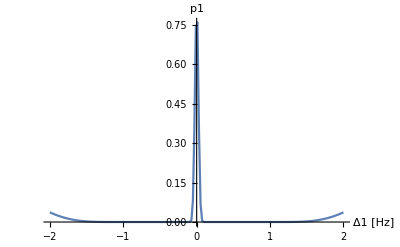

```mathematica
Plot[Abs[p1sq[Δ,Δ][111*10^-6]]^2/. darkRes,{Δ,-2*10^9, 2*10^9}, PerformanceGoal->"Speed", PlotRange->All,AxesLabel->{"Δ1 [Hz]","p1"}]
```

### 3. Stark shift of nearby state

Model the effect of a nearby state at some separation ν from the intermediate as by including Stark shifts of the initial and final states.

```mathematica
dets4 = {Δ -> 0,δ -> 0};
init4 = c[0] == {1,0,0};
c[t_] = {c1[t],c2[t],c3[t]};
T[t_] = {{0,(1/2)*Ωp,0},{(1/2)*Ωp, 2π Δ - ⅈ  2π  γ-  Ωp^2/( 2π (  Δ- ν))/2 ,(1/2)*Ωs},{0,(1/2)*Ωs, 2π δ-Ωp^2/(  2π (Δ-ν))/2+Ωs^2/( 2π (Δ-δ-ν))/2}};
MatrixForm[T[t]]
SEE = ⅈ c'[t] == T[t].c[t];
cSoln= ParametricNDSolve[{SEE /. γ ->10^9/. dets4,init4},{c1,c2,c3},{t,0,10^-3},{t1,w,ν, PS, PP}];
Manipulate[Plot[(δ-Ωp^2/( 2π (Δ-ν))/2+ Ωs^2/( 2π (Δ-δ-ν))/2)/10^6/.dets4 /. {t1->460*10^-6,w-> 30*10^-6, PS -> StokesPower, PP-> PumpPower} ,{t,0,10^-3}, PlotRange->All,AxesLabel->{"t [s]","δ [MHz]"}]Plot[{Evaluate[Abs[c1[450*10^-6,30*10^-6,ν, StokesPower,PumpPower][t]]^2/. cSoln ],Evaluate[Abs[c2[450*10^-6,30*10^-6,ν, StokesPower,PumpPower][t]^2]/. cSoln],Evaluate[Abs[c3[450*10^-6,30*10^-6,ν, StokesPower,PumpPower][t]]^2/. cSoln]},{t,0,10^-3},PlotLegends->{"p1","p2","p3"}, AxesLabel->{"t [s]", Abs[ψ]^2}, PlotRange->All, PerformanceGoal->"Speed"],{ν,0.5*10^9,30*10^9}, {StokesPower, 0.1, 50},{PumpPower, 0.1, 50}]
```

(0 | 1.0273×10^8 ⅇ^(-(0.5 (-1/2000+t)^2)/w^2) √PP | 0
1.0273×10^8 ⅇ^(-(0.5 (-1/2000+t)^2)/w^2) √PP | -2 ⅈ π γ+2 π Δ-(3.35927×10^15 ⅇ^(-(1. (-1/2000+t)^2)/w^2) PP)/(Δ-ν) | 327000000 ⅇ^(-(0.5 (t-t1)^2)/w^2) π √PS
0 | 327000000 ⅇ^(-(0.5 (t-t1)^2)/w^2) π √PS | 2 π δ-(3.35927×10^15 ⅇ^(-(1. (-1/2000+t)^2)/w^2) PP)/(Δ-ν)+(106929000000000000 ⅇ^(-(1. (t-t1)^2)/w^2) π PS)/(-δ+Δ-ν))

ReplaceAll::reps: {dets4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {dets4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {dets4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {dets4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {dets4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {dets4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {dets4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {dets4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {dets4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {dets4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {dets4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(δ-Ωp^2/( 2π (Δ-ν))/2+ Ωs^2/( 2π (Δ-δ-ν))/2)/10^6/.dets4 /. {t1->460*10^-6,w-> 30*10^-6}
```

((3.35927×10^15 ⅇ^(-1.11111×10^9 (-1/2000+t)^2) PP)/ν-(106929000000000000 ⅇ^(-1.11111×10^9 (-23/50000+t)^2) π PS)/ν)/1000000

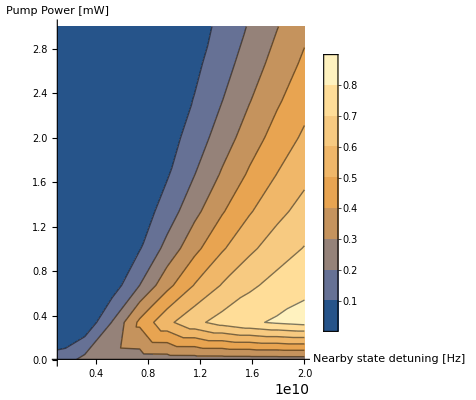

```mathematica
ContourPlot[Evaluate[Abs[c3[450*10^-6,30*10^-6,ν, PumpPower/10,PumpPower][0.001]]^2/. cSoln],{ν,10^9,2*10^10},{PumpPower,0.01,3},PlotLegends->Automatic,Exclusions->None,Axes -> True,Frame->False,AxesLabel->{"Nearby state detuning [Hz]","Pump Power [mW]"},PerformanceGoal->"Speed"]
```

### 4. Master Equation Calculation

**Warning: This section is not properly functional, the von Neumann solver is extremely numerically unstable and does not appear to give reliable results**
An alternative potentially promising approach to this problem is the Monte-Carlo like simulation of phase noise described in https://link.aps.org/doi/10.1103/PhysRevA.65.043409

```mathematica
initρ = ρ[0] =={{1,0,0},{0,0 ,0},{0,0,0}};
ρ[t_] = {{ρ11[t],ρ12[t],ρ13[t]},{ρ21[t],ρ22[t],ρ23[t]},{ρ31[t],ρ32[t],ρ33[t]}};
W[t_] = {{0,(1/2)*Ωp,0},{(1/2)*Ωp, 2π Δ - ⅈ 2π  γ ,(1/2)*Ωs},{0,(1/2)*Ωs, 2π δ}}; (*Effective Hamiltonian including decay*)
L[t_] = {{0,-π Δν ρ12[t],0},{-π Δν ρ21[t],0,-π Δν ρ23[t]},{0,-π Δν ρ32[t], 0}}; (*Finite linewidth Δν coherence decay term*)
Liouv = -ⅈ(W[t].ρ[t] -ρ[t].W[t] )+ L[t];
dets = {Δ -> 0,δ -> 0};
MatrixForm[W[t]]
```

(0 | 1.0273×10^8 ⅇ^(-(0.5 (-1/2000+t)^2)/w^2) √PP | 0
1.0273×10^8 ⅇ^(-(0.5 (-1/2000+t)^2)/w^2) √PP | -2 ⅈ π γ+2 π Δ | 327000000 ⅇ^(-(0.5 (t-t1)^2)/w^2) π √PS
0 | 327000000 ⅇ^(-(0.5 (t-t1)^2)/w^2) π √PS | 2 π δ)

```mathematica
LSoln= ParametricNDSolve[{ρ'[t] == Liouv/. γ ->10^9/. dets,initρ},{ρ11,ρ22,ρ33},{t,0,10^-3},{t1,w, PS, PP,Δν},PrecisionGoal->10, Method -> {"PDEDiscretization" -> {"MethodOfLines", 
      "SpatialDiscretization" -> {"FiniteElement"}}}]; (*The stability is very sensitive to the PrecisionGoal parameter*)
```

ParametricNDSolve::ndsz: At t == 0.000225132, step size is effectively zero; singularity or stiff system suspected.

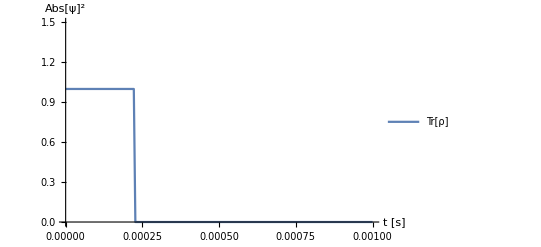

```mathematica
Plot[Evaluate[ρ11[460*10^-6, 30*10^-6, 0.1, 1, 10^3][t] + ρ22[460*10^-6, 30*10^-6, 0.1, 1, 10^3][t]+ρ33[460*10^-6, 30*10^-6, 0.1, 1,  10^3][t]/. LSoln],{t,0,10^-3},PlotLegends->{"Tr[ρ]"}, AxesLabel->{"t [s]", Abs[ψ]^2}, PlotRange->{0,1.5}, PerformanceGoal->"Speed"]
```

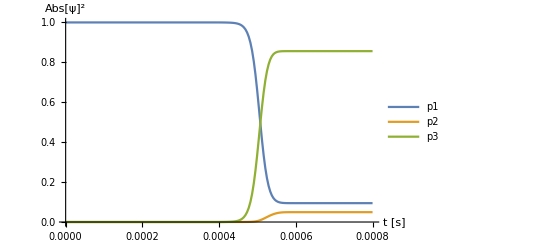

```mathematica
Plot[{Evaluate[ρ11[460*10^-6, 30*10^-6, 0.1, 1,10^10][t]/. LSoln ] ,Evaluate[ρ22[460*10^-6, 30*10^-6, 0.1, 1, 10^10][t]/. LSoln],Evaluate[ρ33[460*10^-6, 30*10^-6, 0.1, 1,10^10][t]/. LSoln]},{t,0,0.8*10^-3},PlotLegends->{"p1","p2","p3"}, AxesLabel->{"t [s]", Abs[ψ]^2}, PlotRange->All, PerformanceGoal->"Speed"]
```